```mathematica
js=Import["Public/goto/files/StepanGC.json"];
```

```mathematica
X={{ToExpression[#⟦1⟧],ToExpression[#⟦2⟧]}&/@("C"/.js),{ToExpression[#⟦1⟧],ToExpression[#⟦2⟧]}&/@("E"/.js)}
```

{{{19,2},{20,2},{21,6},{22,1},{23,6},{24,12},{25,25},{26,31},{27,54},{28,84},{29,118},{30,165},{31,221},{32,257},{33,274},{34,249},{35,261},{36,248},{37,215},{38,197},{39,123},{40,120},{41,82},{42,62},{43,47},{44,43},{45,29},{46,20},{47,14},{48,11},{49,9},{50,3},{51,2},{52,2},{53,2},{54,1},{56,1},{64,1}},{{30,1},{31,4},{32,25},{33,88},{34,259},{35,435},{36,592},{37,621},{38,510},{39,271},{40,142},{41,37},{42,13},{43,2}}}

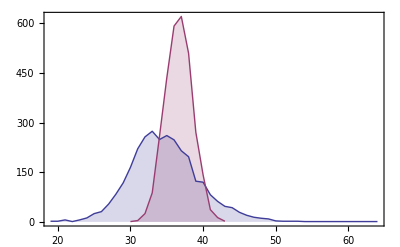

```mathematica
ListPlot[X,Joined->True,Filling->Bottom,Frame->True]
```

```mathematica
X⟦1,1⟧
```

{19,2}

```mathematica
Histogram[X,200,Frame->True]
```

Histogram::ldata: {{{19, 2}, {20, 2}, {21, 6}, {22, 1}, {23, 6}, {24, 12}, {25, 25}, {26, 31}, {27, 54}, {28, 84}, {29, 118}, {30, 165}, {31, 221}, {32, 257}, {33, 274}, {34, 249}, {35, 261}, {36, 248}, « 1 », « 1 », {39, 123}, {40, 120}, {41, 82}, {42, 62}, {43, 47}, {44, 43}, {45, 29}, {46, 20}, {47, 14}, {48, 11}, {49, 9}, {50, 3}, {51, 2}, {52, 2}, {53, 2}, {54, 1}, {56, 1}, {64, 1}}, « 1 »} is not a valid dataset or list of datasets.

Histogram[{{{19,2},{20,2},{21,6},{22,1},{23,6},{24,12},{25,25},{26,31},{27,54},{28,84},{29,118},{30,165},{31,221},{32,257},{33,274},{34,249},{35,261},{36,248},{37,215},{38,197},{39,123},{40,120},{41,82},{42,62},{43,47},{44,43},{45,29},{46,20},{47,14},{48,11},{49,9},{50,3},{51,2},{52,2},{53,2},{54,1},{56,1},{64,1}},{{30,1},{31,4},{32,25},{33,88},{34,259},{35,435},{36,592},{37,621},{38,510},{39,271},{40,142},{41,37},{42,13},{43,2}}},200,Frame→True]

```mathematica
X
```

{{{19,2},{20,2},{21,6},{22,1},{23,6},{24,12},{25,25},{26,31},{27,54},{28,84},{29,118},{30,165},{31,221},{32,257},{33,274},{34,249},{35,261},{36,248},{37,215},{38,197},{39,123},{40,120},{41,82},{42,62},{43,47},{44,43},{45,29},{46,20},{47,14},{48,11},{49,9},{50,3},{51,2},{52,2},{53,2},{54,1},{56,1},{64,1}},{{30,1},{31,4},{32,25},{33,88},{34,259},{35,435},{36,592},{37,621},{38,510},{39,271},{40,142},{41,37},{42,13},{43,2}}}